```mathematica
F[x_]=x^2 Exp[x * Log[10]]
```

10^x x^2

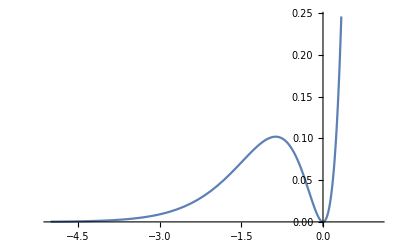

```mathematica
Plot[F[x],{x,-5, 1}]
```

```mathematica
Solve[D[F[x],x]==0]
```

{{x→0},{x→-2/Log[10]}}

```mathematica
N[2/Log[10]]
```

0.868589

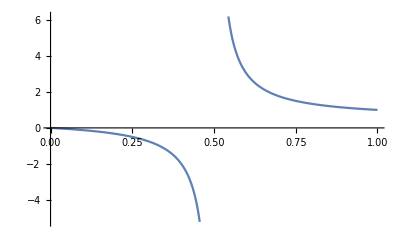

```mathematica
Plot[t/(2t-1),{t,0,1}]
```

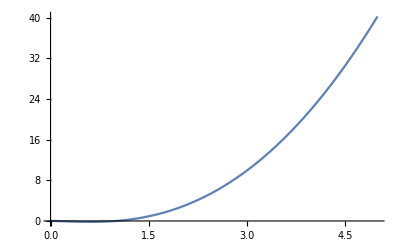

```mathematica
Plot[x^2 Log[x],{x, 0, 5}]
```

```mathematica
P0={1,1};P1={3,3};P2={5,3};P3={4,1};P4={6,2}
```

{6,2}

```mathematica
pts={P0,P1,P2,P3,P4};
Graphics[{BSplineCurve[pts,
SplineKnots->{0,1,1,2,3,4,4,6,8}],
Green, Line[pts], Red, Point[pts]}]
```

-Graphics-

```mathematica
pts={{0,0},{2+√3,0},{1/2,1+(√3)/2},};
weights={};
knots={};
```

```mathematica
pts={{1,0},{1,1},{.5,1},{0,1}};
w={.5,.5,1,.5};
k={0,
0,1/4,1/2,1/2,3/4,
1};
Graphics[
{BSplineCurve[pts,SplineWeights->w,SplineKnots->k],
Blue, Line[pts],
Red,Point[pts]}]
```

-Graphics-

```mathematica
.l
```

-Graphics-

```mathematica
p0={0,0};p1={2+√3,0};p2={1/2,1+(√3)/2};
pts = {p0,p1,p2,p2,p1,p0,p0};
w={1,-Cos[(5Pi)/12],1,1,1,1,1};
knot={0,0,0,1,1,2,2,3,3,3};
Graphics[
{BSplineCurve[pts,
SplineWeights->w,
SplineKnots->knot],
},PlotRange->{{-3,5},{-3,3}}]
```

-Graphics-

```mathematica
p0={0,0};
p3={2+√3,0};
p2={1/2,1+(√3)/2};
p1=p3;
w3=-Cos[(5Pi)/12];
pts = {p0,p1,p2,p3,p3,p0};
w={1,w3,1,1, 1,1};
knot={0,0,0,1,2,2,3,3,3};
Graphics[
{BSplineCurve[pts,
SplineWeights->w,
SplineKnots->knot],
Blue, Line[pts],
Red,Point[pts]},PlotRange->{{-5,5},{-5,5}}]
```

-Graphics-